```mathematica
CompleteSquare[f_,x_]:=Module[{a,b,c},
{c,b,a}=CoefficientList[f,x];
a(x+b/2/a)^2+Simplify[(c-b^2/4/a)]
]

(* Figure out the rotation that puts the signal and idler into the pump coordinates. Here θ is the opening angle and ϕ is the azimuthal angle.
*)

Rx[θ_, V_]:=Module[{S},
RotX =  {{1, 0, 0},{0, Cos[θ],-Sin[θ]}, {0, Sin[θ], Cos[θ]}};
RotX.V
]

Ry[θ_, V_]:=Module[{S},
RotY = {{ Cos[θ],0, +Sin[θ]}, {0,1,0},  {-Sin[θ],0,  Cos[θ]}};
RotY.V
]

Rz[θ_, V_]:=Module[{S},
RotZ := {{ Cos[θ],Sin[θ], 0}, {-Sin[θ], Cos[θ], 0}, {0,0,1}};
RotZ.V
]
```

```mathematica
(* Test for the Migdal Effect coordinates
*)
vv = {1,0,0};
vv1 = Ry[-γ,vv];
vv2 =Rz[-ϕ,vv1];

xprime = vv2;
yprime = Rz[-ϕ,Ry[-γ,{0,1,0}]];
zprime = Rz[-ϕ,Ry[-γ,{0,0,1}]];

(* Rotation Matrix about y'
*)
(*yprime =Refine[ RotationMatrix[θ,{0,0,1}].{0,1,0},Element[θ, Reals]]
RotYprime= RotationMatrix[γ, {x,y,z} ]
RotYprime= Simplify[Refine[RotationMatrix[γ, yprime ], Element[γ, Reals]]]
vv2 = vv2 /. {x1 -> vv1[[1]]*x + vv1[[2]]*y + vv1[[3]]*z}*)

c = Ry[-θ,vv];

pp = Cross[xprime,c]

tanbeta = p.yprime/(p.zprime)
Simplify[p.xprime];


angle = aacross[[2]]/aacross[[3]];
Simplify[angle];
(*ca = CoefficientList[aa,{Cos[β], Sin[β]}];*)
(*ctan = ca[[1,2]]/ca[[2,1]];
Simplify[ctan]*)
Simplify[(-Cos[θ]*Cos[ϕ]*Sin[γ]+Sin[θ]*Cos[γ])/(Cos[θ]*Sin[ϕ])]
Simplify[tanbeta -Simplify[(-Cos[θ]*Cos[ϕ]*Sin[γ]+Sin[θ]*Cos[γ])/(Cos[θ]*Sin[ϕ])]]
```

{Cos[γ] Sin[θ] Sin[ϕ],Cos[θ] Sin[γ]-Cos[γ] Cos[ϕ] Sin[θ],-Cos[γ] Cos[θ] Sin[ϕ]}

(p.{-Sin[ϕ],Cos[ϕ],0})/(p.{-Cos[ϕ] Sin[γ],-Sin[γ] Sin[ϕ],Cos[γ]})

Part::partd: Part specification aacross ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification aacross ⟦ 3 ⟧ is longer than depth of object.

-Cot[ϕ] Sin[γ]+Cos[γ] Csc[ϕ] Tan[θ]

(p.{-Sin[ϕ],Cos[ϕ],0})/(p.{-Cos[ϕ] Sin[γ],-Sin[γ] Sin[ϕ],Cos[γ]})+Cot[ϕ] Sin[γ]-Cos[γ] Csc[ϕ] Tan[θ]

```mathematica
sinbeta = -Cos[θ]*Cos[ϕ]*Sin[γ]+Sin[θ]*Cos[γ];
cosbeta = (Cos[θ]*Sin[ϕ]);

kprime = Rz[Subscript[γ, s],{1,0,0}];
kprime2 = Rx[-β,kprime] //. {Sin[β]->sinbeta, Cos[β]->cosbeta};
poynting = kprime2[[1]]*xprime +kprime2[[2]]*yprime +kprime2[[3]]*zprime;
poynting = Simplify[poynting ]
poynting = Simplify[poynting  //. {γ->0, ϕ->0}];

Rx[-r, {0,y,0}];
```

{Cos[θ] (Cos[ϕ]^2 Sin[γ]^2+Sin[ϕ]^2) Sin[γ_s]+Cos[γ] Cos[ϕ] (Cos[γ_s]-Sin[γ] Sin[θ] Sin[γ_s]),Cos[γ] Sin[ϕ] (Cos[γ_s]-(Cos[γ] Cos[θ] Cos[ϕ]+Sin[γ] Sin[θ]) Sin[γ_s]),Cos[γ_s] Sin[γ]+Cos[γ] (-Cos[θ] Cos[ϕ] Sin[γ]+Cos[γ] Sin[θ]) Sin[γ_s]}

```mathematica
(* These are the normalization coefficients for the three Gaussians
*)

(* To get the signal, we rotate the pump vector about X by Subscript[θ, s], then about Z by Subscript[ϕ, s]
*)

rulescoord ={Subscript[θ, s]->Subscript[θ, i],  Subscript[ϕ, s] ->  Subscript[ϕ, s]+π };
rulescoord2 =  {Subscript[ϕ, ss]-> Subscript[ϕ, s]};
planarrules := {Subscript[ϕ, s] -> 0}
(*rulescoord2 = {Subscript[ϕ, ss] -> Subscript[ϕ, i]};*)

xs = Rz[Subscript[ϕ, s],Rx[Subscript[θ, s],{1,0,0}]];
ys = Rz[Subscript[ϕ, s],Rx[Subscript[θ, s],{0,1,0}]];
zs = Rz[Subscript[ϕ, s],Rx[Subscript[θ, s],{0,0,1}]];

vect = {x,y,z};

Subscript[x, s]=xs.vect
Subscript[y, s]= ys.vect;
Subscript[z, s]=zs.vect;


(*Subscript[x, s] := Cos[Subscript[ϕ, s]]*x -Sin[Subscript[ϕ, s]]*y 
Subscript[y, s]:= Cos[Subscript[θ, s]]*Sin[Subscript[ϕ, s]]*x + Cos[Subscript[θ, s]]*Cos[Subscript[ϕ, s]]*y - Sin[Subscript[θ, s]]*z
Subscript[z, s]:=Sin[Subscript[θ, s]]*Sin[Subscript[ϕ, s]]*x + Sin[Subscript[θ, s]]*Cos[Subscript[ϕ, s]]*y + Cos[Subscript[θ, s]]*z*)


Subscript[x, i] = Subscript[x, s]/.rulescoord
Subscript[y, i]= Subscript[y, s]/.rulescoord
Subscript[z, i]= Subscript[z, s]/.rulescoord

(*Subscript[x, s] = Subscript[x, s] //. planarrules;
Subscript[y, s]= Subscript[y, s]//.planarrules;
Subscript[z, s]= Subscript[z, s]//.planarrules;*)


Subscript[x, p] := x - Subscript[ρ, px]*z
Subscript[y, p]:= y

(*Subscript[x, p] = x;
Subscript[y, p]= y;*)

(* Introduce the assumption that the Rayleigh range is much longer than the crystal length and the waist can be treated as a constant. This dramatically simplifies things.
*)
(*rules2 :={Subscript[q, p] -> Subscript[W, p]^2 , Subscript[q, s] -> Subscript[W, s]^2 , Subscript[q, i] -> Subscript[W, i]^2,  Subscript[θ, s] -> 0*π/180, Subscript[θ, i] ->0*π/180 }*)
 rules2 :={Subscript[q, ppp] -> Subscript[W, ppp]^2 , Subscript[q, s] -> Subscript[W, s]^2 , Subscript[q, i] -> Subscript[W, i]^2 }
 (*rules2 :={Subscript[q, ppp] -> Subscript[W, ppp]^2 , Subscript[q, s] -> Subscript[W, s]^2 , Subscript[q, i] -> Subscript[W, s]^2 }*)

rulesq := rules2
rulesanlge := { Subscript[θ, s] -> 0*π/180, Subscript[θ, i] ->0*π/180}
Subscript[n, s] = Subscript[W, s]/(Sqrt[π*2]*Subscript[q, s]) //.rules2;
Subscript[n, i] = Subscript[W, i]/(Sqrt[π*2]*Subscript[q, i]) //.rules2;
Subscript[n, ppp] = Subscript[W, ppp]/(Sqrt[π*2]*Subscript[q, ppp]) //. rules2;
```

x Cos[ϕ_s]-y Sin[ϕ_s]

-x Cos[ϕ_s]+y Sin[ϕ_s]

-y Cos[θ_i] Cos[ϕ_s]+z Sin[θ_i]-x Cos[θ_i] Sin[ϕ_s]

z Cos[θ_i]+y Cos[ϕ_s] Sin[θ_i]+x Sin[θ_i] Sin[ϕ_s]

```mathematica
(*Here is the argument in the exponential that we will want to integrate over wrt to x, y, and z.
*)
Arg1=-1/(2*Subscript[q, s])*(Subscript[x, s]^2+Subscript[y, s]^2)-1/(2*Subscript[q, i])(Subscript[x, i]^2+Subscript[y, i]^2)-1/(2*Subscript[q, ppp])*(Subscript[x, p]^2+Subscript[y, p]^2) - ⅈ*(Subscript[ΔK, x]*x + Subscript[ΔK, y]*y+Subscript[ΔK, z]*z)
```

-((-x Cos[ϕ_s]+y Sin[ϕ_s])^2+(-y Cos[θ_i] Cos[ϕ_s]+z Sin[θ_i]-x Cos[θ_i] Sin[ϕ_s])^2)/(2 q_i)-((x Cos[ϕ_s]-y Sin[ϕ_s])^2+(y Cos[θ_s] Cos[ϕ_s]+z Sin[θ_s]+x Cos[θ_s] Sin[ϕ_s])^2)/(2 q_s)-ⅈ (x ΔK_x+y ΔK_y+z ΔK_z)-(y^2+(x-z ρ_px)^2)/(2 q_ppp)

```mathematica
(* First we complete the square wrt to x. This makes it easier to analytically carry out the integration.
*)
Arg1 = CompleteSquare[Arg1, x];
{cx,bx,ax}=CoefficientList[Arg1,x];

yzcoeff = Simplify[(cx-bx^2/4/ax)];
coeffx =ax

(* Now complete the square for yz remainder with respect to y
*)

Arg2 = CompleteSquare[yzcoeff, y];
{cy,by,ay}=CoefficientList[Arg2,y];

coeffy = ay;
zint =  Simplify[(cy-by^2/4/ay)];


(*Assuming[Subscript[q, i]>0 && Subscript[q, s]>0 && Subscript[q, p]>0 && Subscript[θ, i]>0 && Subscript[θ, s]>0 && Subscript[ΔK, x] >0 && Subscript[ΔK, y] >0 && Subscript[ΔK, z]>0 &&y>0 &&z>0, Integrate[ Exp[-zint], {z, -∞, ∞}]]*)
```

-Cos[ϕ_s]^2/(2 q_i)-(Cos[θ_i]^2 Sin[ϕ_s]^2)/(2 q_i)-1/(2 q_ppp)-Cos[ϕ_s]^2/(2 q_s)-(Cos[θ_s]^2 Sin[ϕ_s]^2)/(2 q_s)

```mathematica
(* The x and y integrals reduce to the following constants
*)
xconst= Simplify[√π/√(-coeffx) //.rules2];
yconst= Simplify[√π/√(-coeffy) //.rules2];

xonst = xconst /. rulesq ;
yconst = yconst /.rulesq ;
zint2 =Simplify[ zint /. rulesq];

Zexpress =Exp[zint2];

(*This leaves us with just the z integral. Find the coefficients so we can plug it into our solved integral form*)
{az, bz,cz}=CoefficientList[ zint2,z] ;
AA = Simplify[-az];
Simplify[CoefficientList[AA,Subscript[ΔK, x] ]];
Simplify[AA /. {Subscript[W, i]-> Subscript[W, s]}];
BB = Simplify[-bz]
Simplify[CoefficientList[BB,Subscript[ΔK, x] ]];
CC = Simplify[-cz];
```

(ⅈ (4 W_ppp^4 W_s^4 (Sin[2 θ_i] Sin[ϕ_s] ΔK_x+Cos[ϕ_s] Sin[2 θ_i] ΔK_y+2 Cos[θ_i]^2 ΔK_z)+W_i^2 W_ppp^2 W_s^2 (4 W_ppp^2 ((Sin[2 θ_i]-Sin[2 θ_s]) Sin[ϕ_s] ΔK_x+Cos[ϕ_s] (Sin[2 θ_i]-Sin[2 θ_s]) ΔK_y+(2+Cos[2 θ_i]+Cos[2 θ_s]) ΔK_z)+W_s^2 (4 (3+Cos[2 θ_i]) ΔK_z+ΔK_x (4 Sin[2 θ_i] Sin[ϕ_s]+(6+2 Cos[2 θ_i]+Cos[2 (θ_i-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_i+ϕ_s)]) ρ_px)+8 Cos[ϕ_s] Sin[θ_i] ΔK_y (Cos[θ_i]+Sin[θ_i] Sin[ϕ_s] ρ_px)))+W_i^4 (-4 W_ppp^4 (Sin[2 θ_s] Sin[ϕ_s] ΔK_x+Cos[ϕ_s] Sin[2 θ_s] ΔK_y-2 Cos[θ_s]^2 ΔK_z)+8 W_s^4 (ΔK_z+ΔK_x ρ_px)+W_ppp^2 W_s^2 (4 (3+Cos[2 θ_s]) ΔK_z+ΔK_x (-4 Sin[2 θ_s] Sin[ϕ_s]+(6+2 Cos[2 θ_s]+Cos[2 (θ_s-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_s+ϕ_s)]) ρ_px)+8 Cos[ϕ_s] Sin[θ_s] ΔK_y (-Cos[θ_s]+Sin[θ_s] Sin[ϕ_s] ρ_px)))))/(4 (W_ppp^2 W_s^2+W_i^2 (W_ppp^2+W_s^2)) (2 Cos[θ_i]^2 W_ppp^2 W_s^2+2 W_i^2 (Cos[θ_s]^2 W_ppp^2+W_s^2)))

```mathematica
(Subscript[W, i]^2 Subscript[W, ppp]^2 Subscript[W, s]^2 (Subscript[W, ppp]^2 Subscript[W, s]^2 ((6+2 Cos[2 Subscript[θ, i]]+Cos[2 (Subscript[θ, i]-Subscript[ϕ, s])]-2 Cos[2 Subscript[ϕ, s]]+Cos[2 (Subscript[θ, i]+Subscript[ϕ, s])]) Subscript[ΔK, x]^2+8 Sin[Subscript[θ, i]]^2 Sin[2 Subscript[ϕ, s]] Subscript[ΔK, x] Subscript[ΔK, y]+(6+2 Cos[2 Subscript[θ, i]]-Cos[2 (Subscript[θ, i]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, i]+Subscript[ϕ, s])]) Subscript[ΔK, y]^2)+Subscript[W, i]^2 ))/(16 (Subscript[W, ppp]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Subscript[W, ppp]^2+Subscript[W, s]^2)) (Cos[Subscript[θ, i]]^2 Subscript[W, ppp]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, ppp]^2+Subscript[W, s]^2)))
```

{(W_i^2 W_ppp^2 W_s^2 ((6+2 Cos[2 θ_i]-Cos[2 (θ_i-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_i+ϕ_s)]) W_ppp^2 W_s^2+W_i^2 ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) W_ppp^2+8 W_s^2)) ΔK_y^2)/(16 (W_ppp^2 W_s^2+W_i^2 (W_ppp^2+W_s^2)) (Cos[θ_i]^2 W_ppp^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_ppp^2+W_s^2))),(Sin[2 ϕ_s] W_i^2 W_ppp^4 W_s^2 (Sin[θ_s]^2 W_i^2+Sin[θ_i]^2 W_s^2) ΔK_y)/(2 (W_ppp^2 W_s^2+W_i^2 (W_ppp^2+W_s^2)) (Cos[θ_i]^2 W_ppp^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_ppp^2+W_s^2))),(W_i^2 W_ppp^2 W_s^2 ((6+2 Cos[2 θ_i]+Cos[2 (θ_i-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_i+ϕ_s)]) W_ppp^2 W_s^2+W_i^2 ((6+2 Cos[2 θ_s]+Cos[2 (θ_s-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_s+ϕ_s)]) W_ppp^2+8 W_s^2)))/(16 (W_ppp^2 W_s^2+W_i^2 (W_ppp^2+W_s^2)) (Cos[θ_i]^2 W_ppp^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_ppp^2+W_s^2)))}

1/(16 (2 W_ppp^2+W_s^2) ((Cos[θ_i]^2+Cos[θ_s]^2) W_ppp^2+W_s^2))W_ppp^2 W_s^2 (8 W_s^2 (ΔK_x^2+ΔK_y^2)+W_ppp^2 ((12+2 Cos[2 θ_i]+2 Cos[2 θ_s]+Cos[2 (θ_i-ϕ_s)]+Cos[2 (θ_s-ϕ_s)]-4 Cos[2 ϕ_s]+Cos[2 (θ_i+ϕ_s)]+Cos[2 (θ_s+ϕ_s)]) ΔK_x^2-4 (-2+Cos[2 θ_i]+Cos[2 θ_s]) Sin[2 ϕ_s] ΔK_x ΔK_y-(-12-2 Cos[2 θ_i]-2 Cos[2 θ_s]+Cos[2 (θ_i-ϕ_s)]+Cos[2 (θ_s-ϕ_s)]-4 Cos[2 ϕ_s]+Cos[2 (θ_i+ϕ_s)]+Cos[2 (θ_s+ϕ_s)]) ΔK_y^2))

```mathematica
(ⅈ (4 Subscript[W, ppp]^4 Subscript[W, s]^4 (Sin[2 Subscript[θ, i]] Sin[Subscript[ϕ, s]] Subscript[ΔK, x]+Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, i]] Subscript[ΔK, y]+2 Cos[Subscript[θ, i]]^2 Subscript[ΔK, z])+Subscript[W, i]^2 Subscript[W, ppp]^2 Subscript[W, s]^2 (4 Subscript[W, ppp]^2 ((Sin[2 Subscript[θ, i]]-Sin[2 Subscript[θ, s]]) Sin[Subscript[ϕ, s]] Subscript[ΔK, x]+Cos[Subscript[ϕ, s]] (Sin[2 Subscript[θ, i]]-Sin[2 Subscript[θ, s]]) Subscript[ΔK, y]+(2+Cos[2 Subscript[θ, i]]+Cos[2 Subscript[θ, s]]) Subscript[ΔK, z])+Subscript[W, s]^2 (4 (3+Cos[2 Subscript[θ, i]]) Subscript[ΔK, z]+Subscript[ΔK, x] (4 Sin[2 Subscript[θ, i]] Sin[Subscript[ϕ, s]]+(6+2 Cos[2 Subscript[θ, i]]+Cos[2 (Subscript[θ, i]-Subscript[ϕ, s])]-2 Cos[2 Subscript[ϕ, s]]+Cos[2 (Subscript[θ, i]+Subscript[ϕ, s])]) Subscript[ρ, px])+8 Cos[Subscript[ϕ, s]] Sin[Subscript[θ, i]] Subscript[ΔK, y] (Cos[Subscript[θ, i]]+Sin[Subscript[θ, i]] Sin[Subscript[ϕ, s]] Subscript[ρ, px])))+Subscript[W, i]^4 (-4 Subscript[W, ppp]^4 (Sin[2 Subscript[θ, s]] Sin[Subscript[ϕ, s]] Subscript[ΔK, x]+Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, s]] Subscript[ΔK, y]-2 Cos[Subscript[θ, s]]^2 Subscript[ΔK, z])+8 Subscript[W, s]^4 (Subscript[ΔK, z]+Subscript[ΔK, x] Subscript[ρ, px])+Subscript[W, ppp]^2 Subscript[W, s]^2 (4 (3+Cos[2 Subscript[θ, s]]) Subscript[ΔK, z]+Subscript[ΔK, x] (-4 Sin[2 Subscript[θ, s]] Sin[Subscript[ϕ, s]]+(6+2 Cos[2 Subscript[θ, s]]+Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]-2 Cos[2 Subscript[ϕ, s]]+Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[ρ, px])+8 Cos[Subscript[ϕ, s]] Sin[Subscript[θ, s]] Subscript[ΔK, y] (-Cos[Subscript[θ, s]]+Sin[Subscript[θ, s]] Sin[Subscript[ϕ, s]] Subscript[ρ, px])))))

/(4 (Subscript[W, ppp]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Subscript[W, ppp]^2+Subscript[W, s]^2)) (2 Cos[Subscript[θ, i]]^2 Subscript[W, ppp]^2 Subscript[W, s]^2+2 Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, ppp]^2+Subscript[W, s]^2)))
```

```mathematica
{gga, ggb, ggc} = CoefficientList[CC,Subscript[ρ, px]];
Simplify[CC - ggc* Subscript[ρ, px]^2 ]
Simplify[CC - ggc* Subscript[ρ, px]^2 /. {Subscript[W, i]-> Subscript[W, s]}]
Simplify[16 (Subscript[W, ppp]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Subscript[W, ppp]^2+Subscript[W, s]^2)) (Cos[Subscript[θ, i]]^2 Subscript[W, ppp]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, ppp]^2+Subscript[W, s]^2)) /. {Subscript[W, i]-> Subscript[W, s]}]
Simplify[AA /. {Subscript[W, i]-> Subscript[W, s]}]

Simplify[4 Subscript[W, s]^2 ((Cos[Subscript[θ, i]]^2+Cos[Subscript[θ, s]]^2) Subscript[W, ppp]^2+Subscript[W, s]^2) - 2*Subscript[W, s]^2*((2+ Cos[2*Subscript[θ, i]]+ Cos[2*Subscript[θ, s]])*Subscript[W, ppp]^2+2*Subscript[W, s]^2)];

Simplify[-(-2 Sin[Subscript[θ, i]+Subscript[θ, s]]^2 Subscript[W, ppp]^2+Subscript[W, s]^2 (-2+Cos[2 Subscript[θ, i]]+Cos[2 Subscript[θ, s]]+2 (Sin[2 Subscript[θ, i]]-Sin[2 Subscript[θ, s]]) Sin[Subscript[ϕ, s]] Subscript[ρ, px]))/(2 Subscript[W, s]^2 ((2+Cos[2 Subscript[θ, i]]+Cos[2 Subscript[θ, s]]) Subscript[W, ppp]^2+2 Subscript[W, s]^2))+(-2 Sin[Subscript[θ, i]+Subscript[θ, s]]^2 Subscript[W, ppp]^2+Subscript[W, s]^2 (-2+Cos[2 Subscript[θ, i]]+Cos[2 Subscript[θ, s]]+2 (Sin[2 Subscript[θ, i]]-Sin[2 Subscript[θ, s]]) Sin[Subscript[ϕ, s]] Subscript[ρ, px]))/(4 Subscript[W, s]^2 ((Cos[Subscript[θ, i]]^2+Cos[Subscript[θ, s]]^2) Subscript[W, ppp]^2+Subscript[W, s]^2))]

diffC =(Sin[Subscript[θ, i]+Subscript[θ, s]]^2 Subscript[W, ppp]^2+Subscript[W, s]^2 (Sin[Subscript[θ, i]]^2-Sin[2 Subscript[θ, i]] Sin[Subscript[ϕ, s]] Subscript[ρ, px])+Subscript[W, i]^2 (Sin[Subscript[θ, s]]^2+Sin[2 Subscript[θ, s]] Sin[Subscript[ϕ, s]] Subscript[ρ, px]))/(2 (Cos[Subscript[θ, i]]^2 Subscript[W, ppp]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, ppp]^2+Subscript[W, s]^2))) +(-2 Sin[Subscript[θ, i]+Subscript[θ, s]]^2 Subscript[W, ppp]^2+Subscript[W, s]^2 (-2+Cos[2 Subscript[θ, i]]+Cos[2 Subscript[θ, s]]+2 (Sin[2 Subscript[θ, i]]-Sin[2 Subscript[θ, s]]) Sin[Subscript[ϕ, s]] Subscript[ρ, px]))/(2 Subscript[W, s]^2 ((2+Cos[2 Subscript[θ, i]]+Cos[2 Subscript[θ, s]]) Subscript[W, ppp]^2+2 Subscript[W, s]^2)); 

diffA = Simplify[1/(16 (2 Subscript[W, ppp]^2+Subscript[W, s]^2) ((Cos[Subscript[θ, i]]^2+Cos[Subscript[θ, s]]^2) Subscript[W, ppp]^2+Subscript[W, s]^2))Subscript[W, ppp]^2 Subscript[W, s]^2 (8 Subscript[W, s]^2 (Subscript[ΔK, x]^2+Subscript[ΔK, y]^2)+Subscript[W, ppp]^2 ((12+2 Cos[2 Subscript[θ, i]]+2 Cos[2 Subscript[θ, s]]+Cos[2 (Subscript[θ, i]-Subscript[ϕ, s])]+Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]-4 Cos[2 Subscript[ϕ, s]]+Cos[2 (Subscript[θ, i]+Subscript[ϕ, s])]+Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[ΔK, x]^2-4 (-2+Cos[2 Subscript[θ, i]]+Cos[2 Subscript[θ, s]]) Sin[2 Subscript[ϕ, s]] Subscript[ΔK, x] Subscript[ΔK, y]-(-12-2 Cos[2 Subscript[θ, i]]-2 Cos[2 Subscript[θ, s]]+Cos[2 (Subscript[θ, i]-Subscript[ϕ, s])]+Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]-4 Cos[2 Subscript[ϕ, s]]+Cos[2 (Subscript[θ, i]+Subscript[ϕ, s])]+Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[ΔK, y]^2)) - 1/(8 (2 Subscript[W, ppp]^2+Subscript[W, s]^2) ((2+Cos[2 Subscript[θ, i]]+Cos[2 Subscript[θ, s]]) Subscript[W, ppp]^2+2 Subscript[W, s]^2))Subscript[W, ppp]^2 Subscript[W, s]^2 (8 Subscript[W, s]^2 (Subscript[ΔK, x]^2+Subscript[ΔK, y]^2)+Subscript[W, ppp]^2 ((12+2 Cos[2 Subscript[θ, i]]+2 Cos[2 Subscript[θ, s]]+Cos[2 (Subscript[θ, i]-Subscript[ϕ, s])]+Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]-4 Cos[2 Subscript[ϕ, s]]+Cos[2 (Subscript[θ, i]+Subscript[ϕ, s])]+Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[ΔK, x]^2-4 (-2+Cos[2 Subscript[θ, i]]+Cos[2 Subscript[θ, s]]) Sin[2 Subscript[ϕ, s]] Subscript[ΔK, x] Subscript[ΔK, y]-(-12-2 Cos[2 Subscript[θ, i]]-2 Cos[2 Subscript[θ, s]]+Cos[2 (Subscript[θ, i]-Subscript[ϕ, s])]+Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]-4 Cos[2 Subscript[ϕ, s]]+Cos[2 (Subscript[θ, i]+Subscript[ϕ, s])]+Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[ΔK, y]^2))];

diffDen=Simplify[16 (Subscript[W, ppp]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Subscript[W, ppp]^2+Subscript[W, s]^2)) (Cos[Subscript[θ, i]]^2 Subscript[W, ppp]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, ppp]^2+Subscript[W, s]^2)) - 8 (2 Subscript[W, ppp]^2+Subscript[W, s]^2) ((2+Cos[2 Subscript[θ, i]]+Cos[2 Subscript[θ, s]]) Subscript[W, ppp]^2+2 Subscript[W, s]^2) /. {Subscript[W, i]-> Subscript[W, s]}]
```

(Sin[θ_i+θ_s]^2 W_ppp^2+W_s^2 (Sin[θ_i]^2-Sin[2 θ_i] Sin[ϕ_s] ρ_px)+W_i^2 (Sin[θ_s]^2+Sin[2 θ_s] Sin[ϕ_s] ρ_px))/(2 (Cos[θ_i]^2 W_ppp^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_ppp^2+W_s^2)))

-(-2 Sin[θ_i+θ_s]^2 W_ppp^2+W_s^2 (-2+Cos[2 θ_i]+Cos[2 θ_s]+2 (Sin[2 θ_i]-Sin[2 θ_s]) Sin[ϕ_s] ρ_px))/(4 W_s^2 ((Cos[θ_i]^2+Cos[θ_s]^2) W_ppp^2+W_s^2))

8 W_s^4 (2 W_ppp^2+W_s^2) ((2+Cos[2 θ_i]+Cos[2 θ_s]) W_ppp^2+2 W_s^2)

1/(16 (2 W_ppp^2+W_s^2) ((Cos[θ_i]^2+Cos[θ_s]^2) W_ppp^2+W_s^2))W_ppp^2 W_s^2 (8 W_s^2 (ΔK_x^2+ΔK_y^2)+W_ppp^2 ((12+2 Cos[2 θ_i]+2 Cos[2 θ_s]+Cos[2 (θ_i-ϕ_s)]+Cos[2 (θ_s-ϕ_s)]-4 Cos[2 ϕ_s]+Cos[2 (θ_i+ϕ_s)]+Cos[2 (θ_s+ϕ_s)]) ΔK_x^2-4 (-2+Cos[2 θ_i]+Cos[2 θ_s]) Sin[2 ϕ_s] ΔK_x ΔK_y-(-12-2 Cos[2 θ_i]-2 Cos[2 θ_s]+Cos[2 (θ_i-ϕ_s)]+Cos[2 (θ_s-ϕ_s)]-4 Cos[2 ϕ_s]+Cos[2 (θ_i+ϕ_s)]+Cos[2 (θ_s+ϕ_s)]) ΔK_y^2))

0

8 (2 W_ppp^2+W_s^2) ((2+Cos[2 θ_i]+Cos[2 θ_s]) W_ppp^2+2 W_s^2) (-1+W_s^4)

```mathematica
(* While AA, BB, and CC look initially ugly, they simplify down somewhat. This leaves us with real coefficients for z^2 and imaginary coefficents for z. Now, this integral leads to error functions. Instead, look at Taylor expanding what is in the integrand and then carry out the integral.*)

IntResult=Normal[Assuming[aaa>-inf && bbb>-inf && ccc>-inf , Integrate[Series[Exp[-z^2 *(ccc ) -z *(ⅈ*bbb)],{z,0,20}],{z,0,L}]]];
IntResultExact =Normal[Assuming[aaa>-inf && bbb>-inf && ccc>-inf , Integrate[Exp[-z^2 *(ccc ) -z *(ⅈ*bbb)],{z,0,L}]]]
IntResultNoZsq=Simplify[Normal[Assuming[aaa>-inf && bbb>-inf && ccc>-inf , Integrate[Exp[-z *(ⅈ*bbb)],{z,0,L}]]]]

IntResultNoZsq = Exp[ⅈ*bbb*L/2]*Sinc[bbb*L/2]


(*IntResultExact /. {R -> -AA, S -> -BB, T -> -CC}  *)
```

(ⅇ^(-bbb^2/(4 ccc)) √π (Erf[(ⅈ bbb+2 ccc L)/(2 √ccc)]-ⅈ Erfi[bbb/(2 √ccc)]))/(2 √ccc)

(ⅈ (-1+ⅇ^(-ⅈ bbb L)))/bbb

ⅇ^((ⅈ bbb L)/2) Sinc[(bbb L)/2]

```mathematica
Expand[IntResultExact]
```

(ⅇ^(-bbb^2/(4 ccc)) √π Erf[(ⅈ bbb+2 ccc L)/(2 √ccc)])/(2 √ccc)-(ⅈ ⅇ^(-bbb^2/(4 ccc)) √π Erfi[bbb/(2 √ccc)])/(2 √ccc)

0.

(0.+3.95385×10^31 ⅈ) (1.5625×10^-34 (0.+1.99705 ΔK_z)+1.×10^-16 (-2.5×10^-17 (0.-1.99705 ΔK_z)+5.×10^-17 ΔK_z+6.25×10^-18 (0.+15.9882 ΔK_z))+6.25×10^-26 (1.×10^-8 (0.+3.99411 ΔK_z)+2.5×10^-9 (0.+15.9882 ΔK_z)))

294773.

0.767819

0.+2714.65 ⅈ

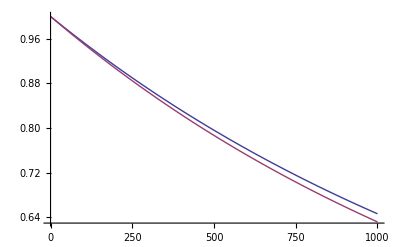

```mathematica
rules2a := { Subscript[θ, s] ->2.2*π/180, Subscript[θ, i] ->2.2*π/180 , Subscript[W, s] -> .00005,Subscript[W, i] -> .0001, Subscript[W, ppp]-> .00005,   Subscript[ΔK, x] ->0,Subscript[ΔK, y] ->0, L -> .001, Subscript[ϕ, s]->0.00000000000, Subscript[ρ, px]->0*π/180}
AA /. rules2a
BB /. rules2a 
CC /. rules2a
IntResult*Exp[-aaa]//. {aaa->AA, bbb->BB, ccc->CC} //.rules2a;
exactResult= IntResultExact/L  //.  {aaa->-AA, bbb->-BB, ccc->CC} //.rules2a;
sincResult = IntResultNoZsq  //.  {aaa->-AA, bbb->BB, ccc->-CC} //.rules2a;


√(2*-ccc)*L //. {aaa->-AA, bbb->BB, ccc->-CC} /.rules2a

BB/2Sqrt[CC] /. rules2a /. {Subscript[ΔK, z] ->10}

nor = exactResult/. {Subscript[ΔK, z] ->0};

Plot[{exactResult/ (nor),sincResult},{Subscript[ΔK, z],0,1000}]
```

```mathematica
(* It looks like I can drop the z^2 term as long as √(2*ccc)*L << 1. Then I can use the straight Gaussian without any problems.
*)
{Subscript[W, s]->0, Subscript[θ, i]->0, Subscript[θ, s]->0}
BB   /.{Subscript[ρ, px]->0, Subscript[W, s]->0, Subscript[ϕ, s]->0}
```

{W_s→0,θ_i→0,θ_s→0}

(ⅈ ((Sin[2 θ_i]-Sin[2 θ_s]) ΔK_y+(2+Cos[2 θ_i]+Cos[2 θ_s]) ΔK_z))/(2+Cos[2 θ_i]+Cos[2 θ_s])

```mathematica
zz = a*z^2 +ⅈ*b*z;
CompleteSquare[zz, z]

f[n_,x_,y_]:=Module[{},
2*x-2*x*Cosh[n*y]*Cos[2*x*y]+n*Sinh[n*y]*Sin[2*x*y]
];

g[n_,x_,y_]:=Module[{},
2*x*Cosh[n*y]*Sin[2*x*y]+n*Sinh[n*y]*Cos[2*x*y]
];


ErfApprox[x_,y_]:=Module[{ans},

ans = Erf[x]+Exp[-x^2]/(2*π*x) *((1-Cos[2*x*y])+ⅈ*Sin[2*x*y])  + 2*Exp[-x^2]/(π)*Sum[Exp[-1/2*n^2]/(n^2+4*x^2) * (f[n,x,y]+ⅈ*g[n,x,y]), {n,1, 100}]
]

val = ⅈ*mm*(ll/(2*mm+mm)) /. {ll->1., mm->.1};
coef =Exp[ll^2/(4*mm)]  /. {ll->.1, mm->.1};;
ErfApprox[Re[val], Im[val]]
Erf[val]
```

b^2/(4 a)+a ((ⅈ b)/(2 a)+z)^2

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

Indeterminate

0.+0.390534 ⅈ

```mathematica
Integrate[Exp[a ((ⅈ b)/(2 a)+z)^2],{z,0,L}]
```

(√π (-ⅈ Erf[b/(2 √a)]+Erfi[√a ((ⅈ b)/(2 a)+L)]))/(2 √a)

```mathematica
ArgS=-1/(2*Subscript[q, s])*(Subscript[x, s]^2+Subscript[y, s]^2)-1/(2*Subscript[q, ppp])*(Subscript[x, p]^2+Subscript[y, p]^2) - ⅈ*(Subscript[ΔK, x]*x + Subscript[ΔK, y]*y+Subscript[ΔK, z]*z);
ArgS = CompleteSquare[ArgS, x];
{cxs,bxs,axs}=CoefficientList[ArgS,x];

yzcoeffs = Simplify[(cxs-bxs^2/4/axs)];
coeffxs =axs

(* Now complete the square for yz remainder with respect to y
*)

ArgS2 = CompleteSquare[yzcoeffs, y];
{cys,bys,ays}=CoefficientList[ArgS2,y];

coeffys = ays;
zints =  Simplify[(cys-bys^2/4/ays)];
```

-1/(2 q_ppp)-Cos[ϕ_s]^2/(2 q_s)-(Cos[θ_s]^2 Sin[ϕ_s]^2)/(2 q_s)

```mathematica
xconsts= Simplify[√π/√(-coeffxs) //.rules2];
yconsts= Simplify[√π/√(-coeffys) //.rules2];

xonsts = xconsts /. rulesq ;
yconsts = yconsts /.rulesq ;
zints =Simplify[ zints /. rulesq];

Zexpress =Exp[zints];

(*This leaves us with just the z integral. Find the coefficients so we can plug it into our solved integral form*)
{azs, bzs,czs}=CoefficientList[ zints,z] ;
AAs = Simplify[-azs]
AA
BBs = Simplify[-bzs];
CCs = Simplify[-czs];

{ggas, ggbs, ggcs} = CoefficientList[CCs,Subscript[ρ, px]];
Simplify[CCs - ggcs* Subscript[ρ, px]^2]
```

(W_ppp^2 W_s^2 (8 W_s^2 (ΔK_x^2+ΔK_y^2)+W_ppp^2 ((6+2 Cos[2 θ_s]+Cos[2 (θ_s-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_s+ϕ_s)]) ΔK_x^2+8 Sin[θ_s]^2 Sin[2 ϕ_s] ΔK_x ΔK_y+(6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) ΔK_y^2)))/(16 (W_ppp^2+W_s^2) (Cos[θ_s]^2 W_ppp^2+W_s^2))

(W_ppp^2 W_s^2 (8 W_s^2 (ΔK_x^2+ΔK_y^2)+W_ppp^2 ((12+2 Cos[2 θ_i]+2 Cos[2 θ_s]+Cos[2 (θ_i-ϕ_s)]+Cos[2 (θ_s-ϕ_s)]-4 Cos[2 ϕ_s]+Cos[2 (θ_i+ϕ_s)]+Cos[2 (θ_s+ϕ_s)]) ΔK_x^2-4 (-2+Cos[2 θ_i]+Cos[2 θ_s]) Sin[2 ϕ_s] ΔK_x ΔK_y-(-12-2 Cos[2 θ_i]-2 Cos[2 θ_s]+Cos[2 (θ_i-ϕ_s)]+Cos[2 (θ_s-ϕ_s)]-4 Cos[2 ϕ_s]+Cos[2 (θ_i+ϕ_s)]+Cos[2 (θ_s+ϕ_s)]) ΔK_y^2)))/(8 (2 W_ppp^2+W_s^2) ((2+Cos[2 θ_i]+Cos[2 θ_s]) W_ppp^2+2 W_s^2))

(Sin[θ_s]^2+Sin[2 θ_s] Sin[ϕ_s] ρ_px)/(2 (Cos[θ_s]^2 W_ppp^2+W_s^2))

```mathematica
(ⅈ (-4 Subscript[W, ppp]^4 (Sin[2 Subscript[θ, s]] Sin[Subscript[ϕ, s]] Subscript[ΔK, x]+Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, s]] Subscript[ΔK, y]-2 Cos[Subscript[θ, s]]^2 Subscript[ΔK, z])+8 Subscript[W, s]^4 (Subscript[ΔK, z]+Subscript[ΔK, x] Subscript[ρ, px])+Subscript[W, ppp]^2 Subscript[W, s]^2 (4 (3+Cos[2 Subscript[θ, s]]) Subscript[ΔK, z]+Subscript[ΔK, x] (-4 Sin[2 Subscript[θ, s]] Sin[Subscript[ϕ, s]]+(6+2 Cos[2 Subscript[θ, s]]+Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]-2 Cos[2 Subscript[ϕ, s]]+Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[ρ, px])+8 Cos[Subscript[ϕ, s]] Sin[Subscript[θ, s]] Subscript[ΔK, y] (-Cos[Subscript[θ, s]]+Sin[Subscript[θ, s]] Sin[Subscript[ϕ, s]] Subscript[ρ, px]))))/(8 (Subscript[W, ppp]^2+Subscript[W, s]^2) (Cos[Subscript[θ, s]]^2 Subscript[W, ppp]^2+Subscript[W, s]^2))
```

(8 W_ppp^2 (Sin[θ_s]^2+Sin[2 θ_s] Sin[ϕ_s] ρ_px+Cos[θ_s]^2 ρ_px^2)+W_s^2 (8 Sin[θ_s]^2+8 Sin[2 θ_s] Sin[ϕ_s] ρ_px+(6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) ρ_px^2))/(16 (W_ppp^2+W_s^2) (Cos[θ_s]^2 W_ppp^2+W_s^2))

(Sin[θ_s]^2+Sin[2 θ_s] Sin[ϕ_s] ρ_px)/(2 (Cos[θ_s]^2 W_ppp^2+W_s^2))

7.13342×10^-9

1.55246×10^-8

0.459492

0.757013

0.+0. ⅈ

275578.

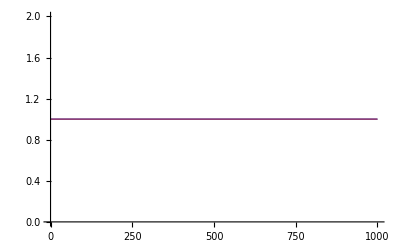

```mathematica
rules2a := { Subscript[θ, s] ->3*π/180, Subscript[θ, i] ->3*π/180 , Subscript[W, s] -> 500*10^-6,  Subscript[W, i] -> 50*10^-6, Subscript[W, ppp]->50*10^-6,   Subscript[ΔK, x] ->0,Subscript[ΔK, y] ->0, Subscript[ΔK, z] ->0, L -> .001, Subscript[ϕ, s]->0.000000000001, Subscript[ρ, px]->0*π/180}
AA /. rules2a;
BB /. rules2a /. {Subscript[ΔK, z] ->0};
CC /. rules2a;
IntResult*Exp[-aaa]//. {aaa->AA, bbb->BB, ccc->CC} //.rules2a;
exactResult= xconst*yconst*IntResultExact/L  //.  {aaa->-AA, bbb->-BB, ccc->CC} //.rules2a
exactResults=xconsts*yconsts*IntResultExact/L  //.  {aaa->-AAs, bbb->-BBs, ccc->CCs} //.rules2a
eff = exactResult/exactResults

sincResult = IntResultNoZsq  //.  {aaa->-AA, bbb->BB, ccc->-CC} //.rules2a;


√(2*-ccc)*L //. {aaa->-AA, bbb->BB, ccc->-CC} /.rules2a
BB/2Sqrt[CC] /. rules2a /. {Subscript[ΔK, z] ->10}

nor = exactResult/. {Subscript[ΔK, z] ->0};
diffC   //.rules2a
Plot[{exactResult/ (nor),sincResult},{Subscript[ΔK, z],0,1000}]
```

```mathematica
.1
```

```mathematica
50*10^-6
```

1/20000